```mathematica
NS["simones_data_gaussianwishart"]
```

```mathematica
clearall
```

ScheduledTaskObject[…]

```mathematica
cov[data_]:={data}.(T@{data})
```

```mathematica
logposterior[x_,data_,nu_,mu_,nn_,tt_]:=Module[{kk=Length[T@data],dim=Length[data],mean=Mean[T@data],nu1,mu1,nn1,tt1,sv,ss},
nu1=nu+kk; nn1=nn+kk;
mu1=(nu*mu+kk*mean)/(nu+kk);
tt1=tt+(data-mean).T[data-mean]+kk*nu/(kk+nu)*(mu-mean).(mu-mean);

sv=nu1-dim+1;
ss=tt1*(nu1+1)/(nu1*sv);

Log[Gamma[(sv+dim)/2]]-Log[Gamma[sv/2]]-dim*Log[sv*Pi]/2-Log[Det[ss]]/2-(sv+dim)*Log[1+(x-mu1).Inverse[ss].(x-mu1)/sv]/2]
```

```mathematica
(datacl={{250,235,272,238,235,250,239,247,253,278,222,292,234},{0.059141,0.124131,0.071957,0.049947,0.133992,0.037906,0.063653,0.02789,0.050404,0.031089,0.025767,0.030121,0.023055}})//MF
```

(250 | 235 | 272 | 238 | 235 | 250 | 239 | 247 | 253 | 278 | 222 | 292 | 234
0.059141 | 0.124131 | 0.071957 | 0.049947 | 0.133992 | 0.037906 | 0.063653 | 0.02789 | 0.050404 | 0.031089 | 0.025767 | 0.030121 | 0.023055)

```mathematica
{datacl,dataclc,datacla}=datafull[[;;,{1,3}]];
```

```mathematica
improp={nu->0,mux->0,muy->0,nn->-1,txx->0,txy->0,tyy->0};
```

```mathematica
ClearAll[logp];logp[x_,y_]=Simplify@logposterior[{x,y},datacl,nu,{mux,muy},nn,{{txx,txy},{txy,tyy}}]/.improp;
```

```mathematica
Exp[logp[1,1]]/.{nu->0,mux->0,muy->0,nn->0,txx->0,txy->0,tyy->0}
```

1.08124×10^-13

```mathematica
Exp[logp[2,3]]
```

1.92355×10^-20

```mathematica
Mean[T@datacl]//N
```

{0.627358,0.64025}

```mathematica
Cov[datacl[[1]],datacl[[2]]]
```

0.00753893

```mathematica
Var[datacl[[1]]]//N
```

0.00853532

```mathematica
Var[datacl[[2]]]//N
```

0.00673052

```mathematica
opa=1
```

1

```mathematica
conh=Plot3D[Exp@logp[x,y],{x,0,1},{y,0,1},PlotStyle->{Opacity[Dynamic[opa]],green},PlotRange->All,BoxRatios->1,PlotPoints->100]
```

-Graphics3D-

```mathematica
dconh=DensityPlot[Exp@logp[x,y],{x,0,1},{y,0,1},ColorFunction->({Opacity[#/2],green}&),PlotRange->All]
```

-Graphics-

```mathematica
contour=Table[i,{i,0,150,10}];
```

```mathematica
opa=15
```

15

```mathematica
thick=100000;
```

```mathematica
cconh=ContourPlot[Exp@logp[x,y],{x,0,1},{y,0,1},Contours->contour,PlotRange->All,ContourShading->None,ContourStyle->Table[{Thickness[i/Dynamic[thick]],green},{i,contour}],PlotLegends->Auto]
```

-Graphics-

```mathematica
opa=0.9
```

0.9

```mathematica
(datacla={{248,189,186,180,256,233,211,215,223,225,256,292,210},{0.045868,0.076175,0.047749,0.064351,0.045629,0.041398,0.022918
,0.026358,0.047857,0.008296,0.026689,0.049821,0.028972}})//MF
```

(248 | 189 | 186 | 180 | 256 | 233 | 211 | 215 | 223 | 225 | 256 | 292 | 210
0.045868 | 0.076175 | 0.047749 | 0.064351 | 0.045629 | 0.041398 | 0.022918 | 0.026358 | 0.047857 | 0.008296 | 0.026689 | 0.049821 | 0.028972)

```mathematica
improp={nu->0,mux->0,muy->0,nn->0,txx->0,txy->0,tyy->0};
```

```mathematica
ClearAll[logpa];logpa[x_,y_]=Simplify@logposterior[{x,y},datacla,nu,{mux,muy},nn,{{txx,txy},{txy,tyy}}]/.improp;
```

```mathematica
Exp[logp[1,1]]/.{nu->0,mux->0,muy->0,nn->0,txx->0,txy->0,tyy->0}
```

1.08124×10^-13

```mathematica
Exp[logp[2,3]]
```

1.92355×10^-20

```mathematica
Mean[T@datacla]//N
```

{224.923,0.0409293}

```mathematica
Cov[datacla[[1]],datacla[[2]]]
```

-0.123699

```mathematica
Var[datacla[[1]]]//N
```

951.609

```mathematica
Var[datacla[[2]]]//N
```

0.000304502

```mathematica
logpa[1,1]
```

-39.0672

```mathematica
cona=Plot3D[Exp@logpa[x,y],{x,0,1},{y,0,1},PlotStyle->{Opacity[Dynamic[opa]],red},PlotRange->All,BoxRatios->1,PlotPoints->100]
```

-Graphics3D-

```mathematica
opa=1
```

1

```mathematica
dcona=DensityPlot[Exp@logpa[x,y],{x,150,350},{y,-0.1,0.2},ColorFunction->({Opacity[#/2],red}&),PlotRange->All]
```

-Graphics-

```mathematica
thick=20;
```

```mathematica
ccona=ContourPlot[Exp@logpa[x,y],{x,0,1},{y,0,1},Contours->contour,PlotRange->All,ContourShading->None,ContourStyle->Table[{Thickness[i/Dynamic[thick]],red},{i,contour}],PlotLegends->Auto]
```

-Graphics-

```mathematica
Show[{cona,conh}]
```

-Graphics3D-

```mathematica
(dataclc={{246,211,226,195,198,235,237,217,301,229,225,236},{0.080927,0.04448,0.051219,0.032039,0.022411,0.024474,0.034872,0.045331,0.13096,0.021884,0.020809,0.044468}})//MF
```

(246 | 211 | 226 | 195 | 198 | 235 | 237 | 217 | 301 | 229 | 225 | 236
0.080927 | 0.04448 | 0.051219 | 0.032039 | 0.022411 | 0.024474 | 0.034872 | 0.045331 | 0.13096 | 0.021884 | 0.020809 | 0.044468)

```mathematica
improp={nu->0,mux->0,muy->0,nn->0,txx->0,txy->0,tyy->0};
```

```mathematica
ClearAll[logpc];logpc[x_,y_]=Simplify@logposterior[{x,y},dataclc,nu,{mux,muy},nn,{{txx,txy},{txy,tyy}}]/.improp;
```

```mathematica
Mean[T@dataclc]//N
```

{229.667,0.0461562}

```mathematica
Cov[dataclc[[1]],dataclc[[2]]]
```

0.650596

```mathematica
Var[dataclc[[1]]]//N
```

685.556

```mathematica
Var[dataclc[[2]]]//N
```

0.000918739

```mathematica
conc=Plot3D[Exp@logpc[x,y],{x,0,1},{y,0,1},PlotStyle->{Opacity[Dynamic[opa]],yellow},PlotRange->All,BoxRatios->1,PlotPoints->100]
```

-Graphics3D-

```mathematica
opa=1;
```

```mathematica
dconc=DensityPlot[Exp@logpc[x,y],{x,150,350},{y,-0.1,0.2},ColorFunction->({Opacity[#/2],yellow}&),PlotRange->All,FrameLabel->myaxes[{"node size","modularity"}],PlotLegends->mylegendsc[{green,yellow,red},{"healthy","MCI","Alzheimer"},Bottom],PlotLabel->mylabels[{"opacity ∝ probability density"}]]
```

-Graphics-

```mathematica
cconc=ContourPlot[Exp@logpc[x,y],{x,0,1},{y,0,1},Contours->contour,PlotRange->All,ContourShading->None,ContourStyle->Table[{Thickness[i/Dynamic[thick]],yellow},{i,contour}],FrameLabel->myaxes[{"graph weights","cluster coeff."}],PlotLegends->mylegendsc[{green,yellow,red},{"healthy","MCI","Alzheimer"},Bottom],PlotLabel->mylabels[{"Line thickness ∝ probability density"}]]
```

-Graphics-

```mathematica
Show[{cona,conc,conh}]
```

-Graphics3D-

```mathematica
bri=10;
```

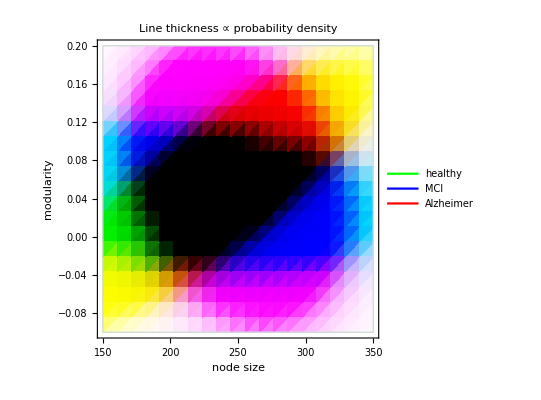

```mathematica
RegionPlot[1<2,{x,150,350},{y,-0.1,0.2},PlotRange->All,ColorFunction->Function[{x,y},ColorNegate@RGBColor[ Exp@logpa[x,y]*bri,Exp@logp[x,y]*bri,Exp@logpc[x,y]*bri]],ColorFunctionScaling->False,FrameLabel->myaxes[{"node size","modularity"}],PlotLegends->mylegendsc[{Green,Blue,Red},{"healthy","MCI","Alzheimer"},Bottom],PlotLabel->mylabels[{"Line thickness ∝ probability density"}]]
```

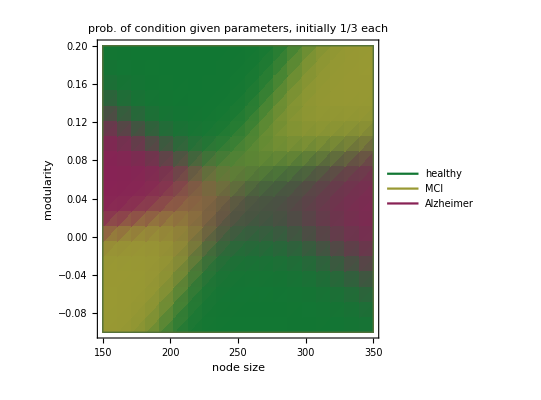

```mathematica
bri=1000;RegionPlot[1<2,{x,150,350},{y,-0.1,0.2},PlotRange->All,ColorFunction->Function[{x,y},Blend[{yellow,green,red},{ Exp@logpc[x,y]*1,Exp@logp[x,y]*1,Exp@logpa[x,y]*1}]],ColorFunctionScaling->False,FrameLabel->myaxes[{"node size","modularity"}],PlotLegends->mylegendsc[{green,yellow,red},{"healthy","MCI","Alzheimer"},Bottom],PlotLabel->mylabels[{"prob. of condition given parameters, initially 1/3 each"}]]
```

```mathematica
expdfr["claudia_nodesize_modularity2b"]
```

../work/claudia_nodesize_modularity2b.pdf

```mathematica
Show[{dcona,dconc,dconh}]
```

-Graphics-

```mathematica
Show[{dconc,dconh,dcona}]
```

-Graphics-

```mathematica
expdfr["claudia_nodesize_modularity2"]
```

../work/claudia_nodesize_modularity2.pdf

```mathematica
Show[{cconc,cconh,ccona}]
```

-Graphics-

```mathematica
expdf["claudia_nodesize_modularity1"]
```

../work/claudia_nodesize_modularity1.pdf

```mathematica
opa=20
```

20

```mathematica
(* Test of correctness of t-distribution as integral of gaussian-wishart *)
```

```mathematica
mm={RandomReal[],RandomReal[]};nu=RandomReal[]+1;nn=RandomReal[]+1;jj=RandomReal[{0,1},{2,2}];sigma=jj.T[jj];
```

```mathematica
lambda=Inverse[{{la11,la12},{la12,la22}}];mu={mu1,mu2};
```

```mathematica
ClearAll[integrand];integrand[x_]:=Exp[-(x-mu).lambda.(x-mu)/2]*Sqrt[Det[lambda/(2*Pi)]]*
Sqrt[Det[nu*lambda/(2*Pi)]]*Exp[-nu*(mu-mm).lambda.(mu-mm)/2]*
Det[lambda]^((nn-Length[x]-1)/2)*Exp[-Tr[lambda.sigma]/2]*Det[sigma/2]^(nn/2)/Product[Pi^((Length[x]-1)/4)*Gamma[(nn-ii)/2],{ii,0,Length[x-1]}]
```

```mathematica
tstudent[x_]:=Gamma[(nn+1)/2]/Gamma[(nn-Length[x]+1)/2]/Sqrt@Det[sigma*(nu+1)/nu*Pi]*(1+(x-mm).Inverse[sigma*(nu+1)/nu].(x-mm))^(-(nn+1)/2)
```

```mathematica
ClearAll[inte];inte[x_,y_]=Simplify@integrand[{x,y}];
```

```mathematica
inte[1,2]
```

-1/((1/(-la12^2+la11 la22))^0.112586)9.24462×10^-7 ⅇ^((la22 (1.50146-2.57086 mu1+1.42856 mu1^2)+la12 (-2.50958+mu1 (2.32918-2.85712 mu2)+2.57086 mu2)+la11 (2.07017-2.32918 mu2+1.42856 mu2^2))/(1. la12^2-1. la11 la22)) √(-1./(1. la12^2-1. la11 la22))

```mathematica
Install["Cuba\\Cuhre"];Install["Cuba\\Suave"];Install["Cuba\\Vegas"];Install["Cuba\\Divonne"];
```

```mathematica
NIntegrate[inte[1,2],{mu1,-Infinity,Infinity},{mu2,-Infinity,Infinity},{la11,0,+Infinity},{la22,0,+Infinity},{la12,-Sqrt[la11*la22],+Sqrt[la11*la22]}]
```

$Aborted

```mathematica
Cuhre[inte[1,2],{mu1,-10^6,10^6},{mu2,-10^6,10^6},{la11,0,+10^6},{la22,0,+10^6},{la12,-Sqrt[la11*la22],+Sqrt[la11*la22]}]
```

{{6.78267×10^-292,0.,0.00272106}}

```mathematica
tstudent[{1,2}]
```

0.000193892

```mathematica
Cuhre[tstudent[{x,y}],{x,-10^6,10^6},{y,-10^6,10^6}]
```

{{0.999775,0.0301379,0.}}

```mathematica
inte[1,2]
```

1/((1/(-la12^2+la11 la22))^0.75224)0.0000586384 ⅇ^((la22 (1.07315-1.44739 mu1+1.10029 mu1^2)+la12 (-2.27136+mu1 (2.11098-2.20058 mu2)+1.44739 mu2)+la11 (2.08002-2.11098 mu2+1.10029 mu2^2))/(1. la12^2-1. la11 la22)) √(-1./(1. la12^2-1. la11 la22))

```mathematica
wishart
```

```mathematica
repl={mm->mm0,nu->nu0,nn->nn0,sigma->sigma0};
```

```mathematica
inte[{x_,y_}]=Simplify[integrand[{x,y}]/.repl]
```

{}